# Assignment 3

## Group 4

Jordan Earle - 12297127, Martin Frassek - 12236632

## Introduction

Often when biomolecular systems become complex, they cannot be reduced to elementary properties of the individual components, therefor mathematical models are often applied to the systems to understand and predict cellular functions.

## Exercise 1

### Background and Theory

Hi this is text

### Results and Discussion

#### A1

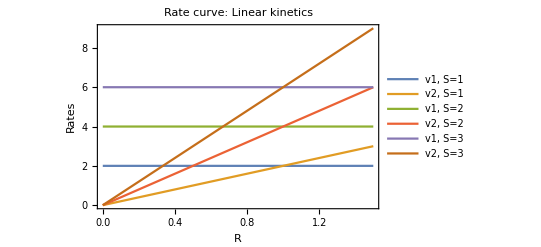

```mathematica
rateconsta = {k1 -> 2, k2 -> 2, k3 -> 1, k4 -> 1};
x = k3*s/k4;
ratesa = {v1 -> k1*s, v2 -> k2*x*r};

Plot[{
v1/.ratesa/.rateconsta/.s->1,
v2/.ratesa/.rateconsta/.s->1,
v1/.ratesa/.rateconsta/.s->2,
v2/.ratesa/.rateconsta/.s->2,
v1/.ratesa/.rateconsta/.s->3,
v2/.ratesa/.rateconsta/.s->3},

{r,0,1.5},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v2, S=1", "v1, S=2", "v2, S=2", "v1, S=3", "v2, S=3"}, 
PlotLabel->Style["Rate curve: Linear kinetics", FontSize->18] ]
```

You can plot it and it would show  a constant response independent of the signal, which will be approximately 1.

#### A2

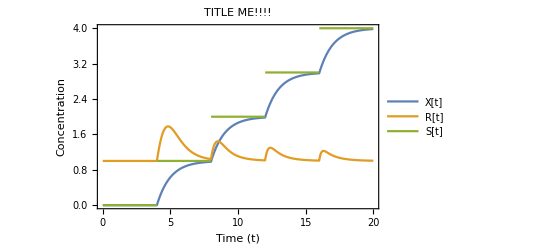

```mathematica
ClearAll["Global`*"];

s[t_] = Floor[t/4];

sol = NDSolve[Evaluate[{x'[t] == (1*s[t]) - (1*x[t]), r'[t] == (2*s[t]) - (2*x[t]*r[t]),r[0] == 1,x[0] == 0}], {x[t], r[t]}, {t, 0, 20}];
Plot[{x[t]/.sol, r[t]/.sol, s[t]}, {t,0,20},
Frame->True,FrameLabel->{"Time (t)","Concentration"},
PlotLegends -> {"X[t]","R[t]","S[t]"},
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

#### B1

Negative Feedback

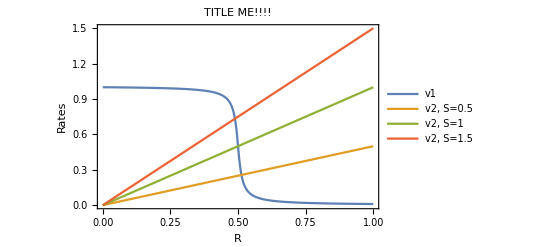

```mathematica
ClearAll["Global`*"];

G[u_, v_, J_, K_] := (2*u*K)/ (v-u+v*J+u*K+√((v-u+v*J+u*K)^2 - 4(v-u)*u*K))

rateconstb = {k0 -> 1, k2 -> 1, k3 -> 0.5, k4 -> 1, J3 -> 0.01, J4 -> 0.01 };

ratesb = {v1 -> k0*G[k3,k4*R,J3,J4]/.rateconstb, v2 -> k2*S*R};

Plot[{
v1/.ratesb/.rateconstb,
v2/.ratesb/.rateconstb/.S->0.5,
v2/.ratesb/.rateconstb/.S->1,
v2/.ratesb/.rateconstb/.S->1.5,
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

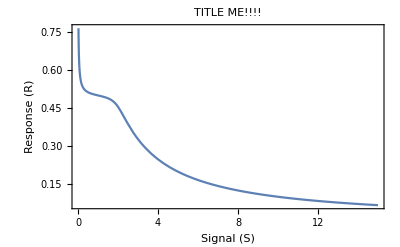

```mathematica
solb = Solve[0 == (v1-v2)/.ratesb,R][[1]][[1]][[2]];
Plot[solb/.rateconstb, 
{S,0,15},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

Positive feedback: Mutual Inhibition

S

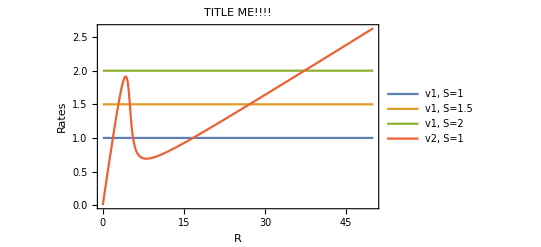

```mathematica
rateconstc = {k0 -> 0, k1 -> 1, k2 -> 0.05, k2nd -> 0.5, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesc = {v1 -> k0 + k1*S, v2 -> k2*R + k2nd*R*G[k3,k4*R,J3,J4]/.rateconstc};

v1/.ratesc/.rateconstc(*/.S->1*)

Plot[{
v1/.ratesc/.rateconstc/.S->1,
v1/.ratesc/.rateconstc/.S->1.5,
v1/.ratesc/.rateconstc/.S->2,
v2/.ratesc/.rateconstc
},

{R,0,50},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v1, S=1.5", "v1, S=2", "v2, S=1", "v2, S=1.5", "v2, S=2"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

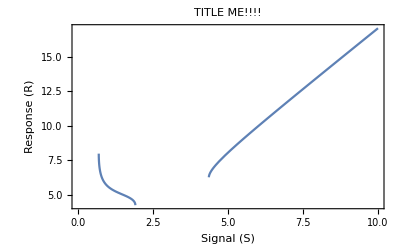

```mathematica
solc = Solve[0 == (v1-v2)/.ratesc,R][[1]][[1]][[2]];
Plot[solc/.rateconstc, 
{S,0,10},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

Positive Feedback: Mutual Activation

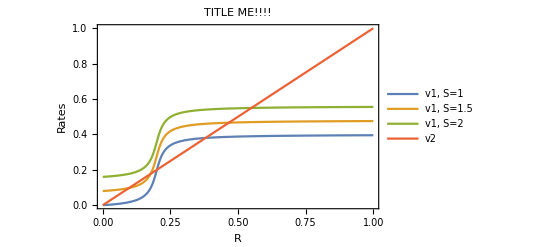

```mathematica
rateconstd = {k0 -> 0.4, k1 -> 0.01, k2 -> 1, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesd = {v1 -> k0*G[k3*R, k4, J3, J4]+k1*S, v2 -> k2*R};

Plot[{
v1/.ratesd/.rateconstd/.S->0,
v1/.ratesd/.rateconstd/.S->8,
v1/.ratesd/.rateconstd/.S->16,
v2/.ratesd/.rateconstd
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v1, S=1.5", "v1, S=2", "v2"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

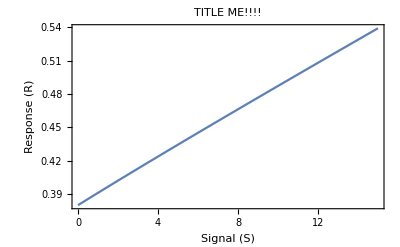

```mathematica
sold = Solve[0 == (v1-v2)/.ratesd,R][[1]][[1]][[2]];
Plot[sold/.rateconstd, 
{S,0,15},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

B1.b
Explain why in the homeostatic system, graphs 1, the response values are confined to a narrow window.....  They dont appear to be....

## Exercise 2

## Exercise 3

### Background and Theory

Hi this is text

### Results and Discussion

The bollean network was defined as:
-Graphics-
where 3 components can influence each other.  This occurs by X and Z activating Y, Y activating Z, Z inactivating X and X activating itself.  For such a simple system the  rules for the system can be defined as follows.

Rules
- X(t+1) = 0 	if 	Z(t)
- X(t+1) = 1 	if 	NOT Z(t) AND X(t)
- Y(t+1) = 0 	if 	NOT (X(t) AND Z(t))
- Y(t+1) = 1 	if 	X(t) AND Z(t)
- Z(t+1) = 0 	if 	NOT Y(t)
- Z(t+1) = 1 	if 	Y(t)

From this a state transition table can be constructed which takes into consideration all previous states and the resulting states at the next time step.  This can written out as it is a simple system, and can be seen in the following table.

X(t) | Y(t) | Z(t) |   | X(t+1) | Y(t+1) | Z(t+1)
0 | 0 | 0 |   | 1 | 0 | 0
1 | 0 | 0 |   | 1 | 0 | 0
0 | 1 | 0 |   | 1 | 0 | 1
0 | 0 | 1 |   | 0 | 0 | 0
1 | 1 | 0 |   | 1 | 0 | 1
1 | 0 | 1 |   | 0 | 1 | 0
0 | 1 | 1 |   | 0 | 0 | 1
1 | 1 | 1 |   | 0 | 1 | 1

In order to confirm these results, this was also found using mathematica.  This table can be seen in the following table.

```mathematica
ClearAll["Global`*"];
(*Define the rules as above. For X = 0 -> a0, X = 1-> a1, ..., etc. *)
x0[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][Z]],0]
x1[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][Z]]&&Interpreter["Boolean"][X],1]
y0[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][X]]&&Not[Interpreter["Boolean"][Z]],0]
y1[X_,Y_,Z_]:=If[Interpreter["Boolean"][X]&&Interpreter["Boolean"][Z],1]
z0[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][Y]],0]
z1[X_,Y_,Z_]:=If[Interpreter["Boolean"][Y],1]

(*Null values are generated, which have to be set to the value zero*)
x[X_, Y_, Z_]:=Apply[x0,{X, Y, Z}]/.Null->0 + Apply[x1, {X, Y, Z}]/.Null->0;
y[X_, Y_, Z_]:=Apply[y0,{X, Y, Z}]/.Null->0 + Apply[y1, {X, Y, Z}]/.Null->0;
z[X_, Y_, Z_]:=Apply[z0,{X, Y, Z}]/.Null->0 + Apply[z1,{X, Y, Z}]/.Null->0;

(*Generate a list of all possible states*)
statesList = Tuples[{{0,1},{0,1},{0,1}}];

(*Apply the rules to this states list*)
listTransition = Catenate[{statesList//Transpose,{ Apply[x, statesList,1], Apply[y, statesList,1], Apply[z, statesList,1]}}]//Transpose;

(*Make a nice readable table*)
TableForm[listTransition,TableHeadings->{Automatic,{"X(t)","Y(t)","Z(t)","X(t+1)","Y(t+1)","Z(t+1)"}},TableAlignments->Center]
```

| X(t) | Y(t) | Z(t) | X(t+1) | Y(t+1) | Z(t+1)
1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 1 | 0 | 0 | 0
3 | 0 | 1 | 0 | 0 | 0 | 1
4 | 0 | 1 | 1 | 0 | 0 | 1
5 | 1 | 0 | 0 | 0 | 0 | 0
6 | 1 | 0 | 1 | 0 | 1 | 0
7 | 1 | 1 | 0 | 0 | 0 | 1
8 | 1 | 1 | 1 | 0 | 1 | 1

This is the state transition graph

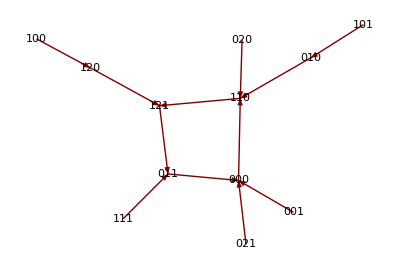

```mathematica
GraphPlot[{"000"->"110","001"->"000","010"->"110","011"-> "000",
"020"->"110","021"->"000","100"->"120","101"->"010","110"->"121",
"111"->"011","120"->"121","121"->"011"},DirectedEdges->True,VertexLabeling->All]
```